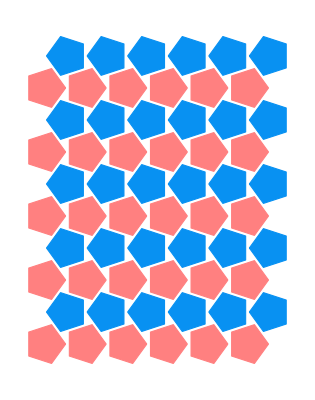

```mathematica
c = 1.1;
d1 = 1+Cos[Pi/5];
d2 = 3Sin[2Pi/5];
px = (1/2+Cos[2Pi/5]+1/2Cos[2Pi/5]);
py = 3/2Sin[2Pi/5];
Centers1 = Flatten[Table[{n1*d1*c,n2*d2*c},{n1,0,5},{n2,0,4}],1];
Centers2 = Table[Centers1[[i]] + c*{px,py},{i,1,Length[Centers1]}];
R = {{Cos[2Pi/5],-Sin[2Pi/5]},{Sin[2Pi/5],Cos[2Pi/5]}};
Vertices1= Table[Table[Centers1[[i]]+MatrixPower[R,n].{1,0},{n,0,4}],{i,1,Length[Centers1]}];
Vertices2 = Table[Table[Centers2[[i]]+MatrixPower[R,n].{-1,0},{n,0,4}],{i,1,Length[Centers2]}];

P1=Table[Graphics[{EdgeForm[Thick],Pink,Polygon[Vertices1[[i]]]}],{i,1,Length[Vertices1]}];
P2=Table[Graphics[{EdgeForm[Thick],RGBColor[0.03,0.57,0.95],Polygon[Vertices2[[i]]]}],{i,1,Length[Vertices2]}];

Show[P1,P2]
```